Autor: Krzysztof Dragon

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 9

Metoda odchyłek ważonych

Napisać procedurę realizującą metodę odchyłek ważonych dla równania:

u''(x)-3u'(x)=4x,   x∈(2,3),

z warunkami brzegowymi:

u(2)=0,
u(3)=0.

Przyjąć, że funkcje kształtu będą spełniały zadane warunki brzegowe.

a) Korzystając z napisanej procedury wyznaczyć metodą Galerkina rozwiązanie przybliżone przyjmując jako funkcje kształtu:

Φ_1(x)=(x-2)(x-3),   
Φ_2(x)=x(x-2)(x-3).

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązanie przybliżone. Policzyć także normę (w L^2) różnicy pomiędzy rozwiązaniem dokładnym i przybliżonym (wynik podać w postaci ułamka dziesiętnego).

b) Wykonać te same obliczenia dla trzech funkcji kształtu:

Φ_1(x)=(x-2)(x-3),   
Φ_2(x)=x(x-2)(x-3),   
Φ_3(x)=x^2(x-2)(x-3).

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązanie przybliżone. Policzyć także normę (w L^2) różnicy pomiędzy rozwiązaniem dokładnym i przybliżonym (wynik podać w postaci ułamka dziesiętnego).

## Rozwiązanie

```mathematica
Clear[mow];
mow[ϕ_,w_,n_,z_Symbol]:= Module[{a,b,t,x,i,pp,p,r,rownania,roz,tr},
a=2;
b=3;
pp = Array[p,n];
t[x_]:= ∑_(i=1)^n pp[[i]]*ϕ[i][x];
r[0][x_]:= (D[t[xx],{xx,2}] /. {xx -> x}) -3*(D[t[xx],xx]/.{xx->x}) - 4*x;
rownania = Table[∫_a^b (w[i][x]*r[0][x])ⅆx==0,{i,1,n}];
roz = Solve[rownania];
tr = Simplify[t[z] /. roz[[1]]];
Return[tr]
]
```

```mathematica
(* Zadanie 1 podpunkt a *)
```

```mathematica
ydok = DSolve[{u''[x]-3u'[x]-4x ==0,u[2]==0,u[3]==0},u[x],x];
```

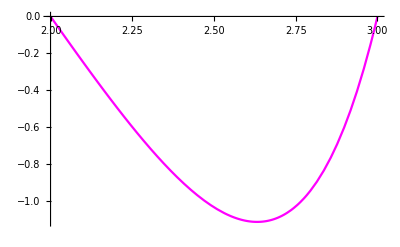

```mathematica
pltdok = Plot[u[x] /. ydok,{x,2,3}, PlotStyle->Magenta]
```

```mathematica
(* Funkcje kształtu *)
ϕ[1][x_]:= (x-2)(x-3);
ϕ[2][x_] := x(x-2)(x-3);
ϕ[3][x_] := x^2(x-2)(x-3);
```

```mathematica
n = 2;
funkcja1 = mow[ϕ,ϕ,n,z]
```

4/69 (-834+1205 z-564 z^2+85 z^3)

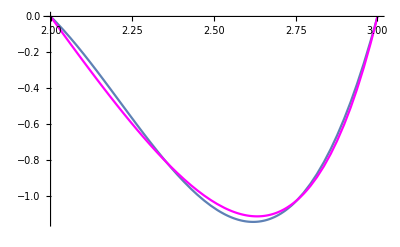

```mathematica
plt1 = Plot[funkcja1,{z,2,3}];
Show[plt1,pltdok]
```

```mathematica
(* Norma L^2 *)
norma = N[∫_2^3 Abs[ϕ[x]]^2ⅆx];
```

NIntegrate::inumr: The integrand Abs[ϕ[x]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{2,3}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
(* Podpunkt b *)
n = 3;
funkcja2 = mow[ϕ,ϕ,n,z]
```

1/6 (516-892 z+597 z^2-182 z^3+21 z^4)

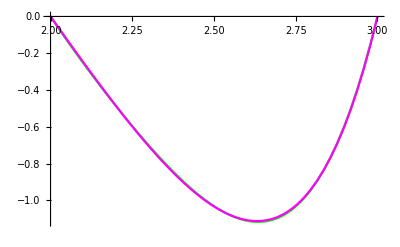

```mathematica
plt2=Plot[funkcja2,{z,2,3}, PlotStyle->Green];
Show[plt2,pltdok]
```